# POSETS : A Mathematica Package PART 2: More Complicated Examples

Curtis Greene, Eugenie Hunsicker, Department of Mathematics, Haverford College 19041, July 1990
Updates 1992-94:  John Dollhopf, Sam Hsiao, Curtis Greene
Updates 2008:  Erica Greene, Curtis Greene
Updates 2010-2012:  Ian Burnette, Curtis Greene

## 0. Introduction

Part 1 of the documentation contains examples illustrating the basic commands. Part 2 (this notebook) contains more complicated examples and several "case studies" illustrating applications to various problems in combinatorics.

The package should be run first, e.g., by entering

```mathematica
<<posets300.m
```

or by opening the document and clicking on the "run package" button.

## 6. Sandpile Posets

The "sandpile posets" are a class of posets related to both  chip-firing posets and majorization posets (MajP[n]).  Essentially, the covering relation is defined as in the majorization lattice, except that only adjacent elements may be transformed. The commands defining these posets are built into the package,  but are included here as an illustration.

```mathematica
SOrder[w_]:=Module[{outlist={},i},
    If[w[[-1]]>=2,AppendTo[outlist, Join[Drop[w,-1], Join[{w[[-1]]-1}, {1}]]]];
    Do[
       If[w[[i]]-w[[i+1]]>1&& w[[i]]>0 , AppendTo[outlist,Adjust[i,w]]],
       {i,Length[w]-1}];
   outlist
];

Adjust[j_,w_]:= Module[{t=w},
	 t[[j]]=w[[j]]-1;t[[j+1]]= w[[j+1]]+1; 
t];
          
SPM[n_] := {SOrder,{{n}},n^4};
```

Building poset spm9  ...

Done

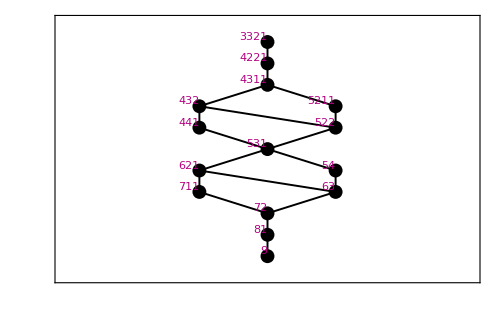

```mathematica
Build[SPM[9],spm9]
ChangeLabel[spm9,Compact,1]
Diagram[spm9,ShowLabels->1]
```

Technically, the sandpile poset is the dual of what we have just constructed.

Building poset dspm9  ...

Done

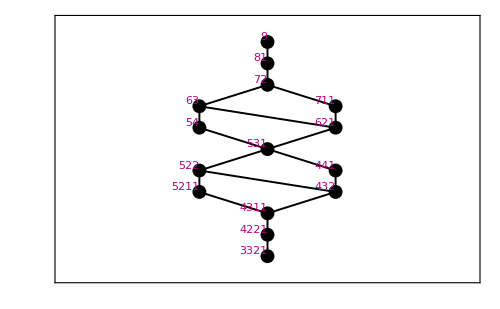

```mathematica
BuildDual[spm9,dspm9]
ChangeLabel[dspm9,Compact,1]
Diagram[dspm9,ShowLabels->1]
```

```mathematica
LatticeQ[spm9]
DistributiveLatticeQ[spm9]
```

True

True

The sandpile posets are always lattices, but (unfortunately) not always distributive.

Building poset spm10  ...

Done

Building poset dspm10  ...

Done

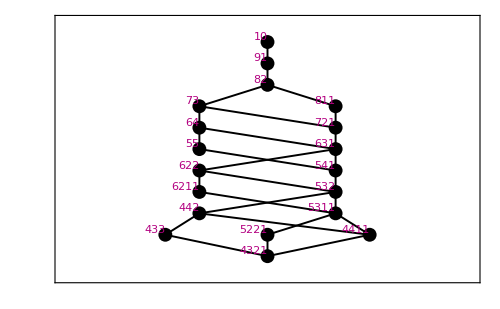

```mathematica
Build[SPM[10],spm10]
BuildDual[spm10,dspm10]
ChangeLabel[dspm10,Compact,1]
Diagram[dspm10,ShowLabels->1]
```

```mathematica
LatticeQ[dspm10]
DistributiveLatticeQ[dspm10]
```

True

False

Is it an interval in the majorization order?

```mathematica
Build[MajP[10],majp10]
RankedQ[majp10]
spindices=LocateSet[majp10,P[dspm10]]
IntervalQ[majp10,spindices]
```

Building poset majp10  ...

Done

False

{22,23,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42}

False

The answer appears to be "no".  Let' s look at the situation a little more carefully. Output from the Diagram command is not particularly useful, but it is possible to see much more using the Manipulate option.  (Try it yourself, shrinking the dots, shifting, stretching, zooming, etc.)

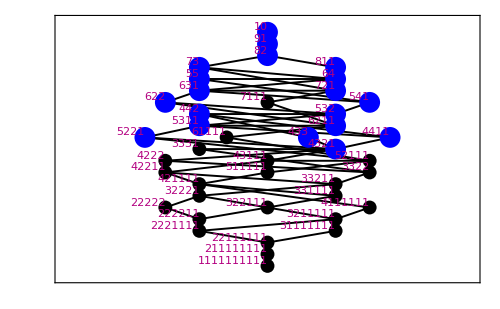

12345

```mathematica
ChangeLabel[majp10,Compact,1]
Diagram[majp10,spindices,ShowLabels->1]
Diagram[majp10,spindices,Manipulate->True]
```

Here is a "blown-up" version of the diagram, created using the Diagram/Manipulate command.

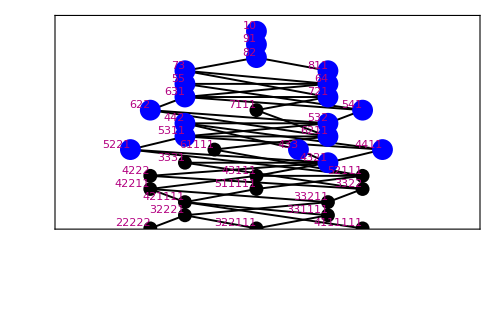

```mathematica
Diagram[majp10,spindices,ShowLabels->1]
```

If you explore the diagram carefully you will see that the sandpile lattice is not an interval: the partition (6, 2, 1, 1) is in the sandpile poset, i.e. it can be obtained from (10) by sandpile operations. On the other hand, (7, 1, 1, 1) lies above it in the majorization order, but does not lie in the sandpile poset.

## 7. Fibonacci Lattices

The r-Fibonacci lattice,  denoted by Fib(r), is defined as follows. Let A(r) = {0,1,...,r}, and let A(r)* denote the set of all finite words formed from letters in A(r).  Define Fib(r) by taking A(r)* as the underlying set, and letting v cover u if u can be obtained from v by changing a 0 in v to an x≠0 or by removing the last digit in v if it is non-zero. It is clear that Fib(r) is a graded poset with a unique minimal element. Furthermore, when r = 1, the number of elements at rank n is the Fibonacci number Fn+1 (where F1= F2=1, Fn+1=Fn + Fn–1).

The first step is to define the covering function for Fib(r). Here fiblattice[r,h] returns a triple {fibcover, {{}}, h}, where fibcover is the covering function (depending on r), {} is the unique minimal element (the empty word), and h is the the rank up to which we wish to build Fib(r). Thus, applying Build to fiblattice[r,h] yields Fib(r) "up to" rank h.

```mathematica
fiblattice[r_,h_]:=Block[{},fibcover[w_]:=Block[{coverlist={},len=Length[w]},Do[AppendTo[coverlist,Flatten[{w,i}]],{i,r}];Do[If[!(w⟦i⟧==0),AppendTo[coverlist,Join[Take[w,i-1],{0},Take[w,-(len-i)]]]],{i,len}];coverlist];Return[{fibcover,{{}},h}];];
```

Building poset fib105  ...

Done

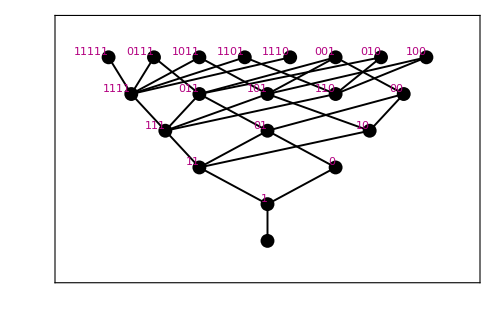

```mathematica
Build[fiblattice[1,5],fib105]
ChangeLabel[fib105,Compact,1];
Diagram[fib105,ShowLabels->1]
```

```mathematica
NK[fib105]
```

{1,1,2,3,5,8}

The poset we have constructed is obviously not a lattice, because we have constructed only finitely many ranks.  However, the principal order ideals in Fib[r] are lattices. In fact when r=1 they are distributive lattices.

{1,2,3,5,7,8,10,15}

Building Subposet ideal105  ...

Building poset ideal105  ...

Done

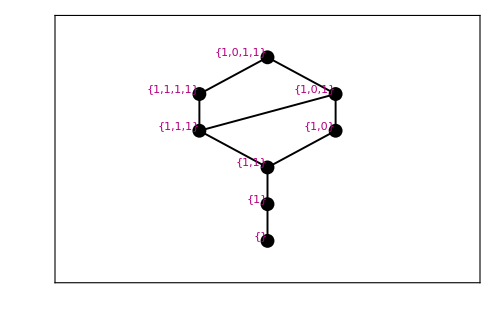

```mathematica
indices=IntervalP[fib105,{},{1,0,1,1}]
BuildSubPoset[fib105,indices,ideal105]
Diagram[ideal105,ShowLabels->1]
```

```mathematica
DistributiveLatticeQ[ideal105]
```

True

Next we construct Fib[2].

Building poset fib203  ...

Done

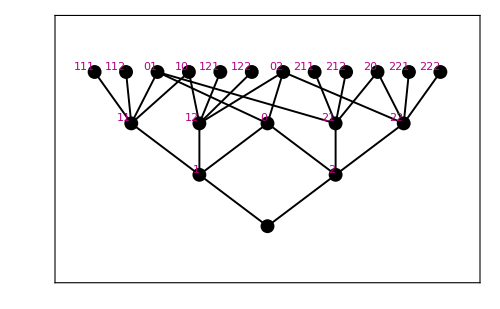

```mathematica
Build[fiblattice[2,3],fib203]
ChangeLabel[fib203,Compact,1]
Diagram[fib203,ShowLabels->1]
```

```mathematica
Build[fiblattice[2,5],fib205]
Diagram[fib205,Manipulate->True];
```

Building poset fib205  ...

Done

```mathematica
RGF[fib205]
```

1+2 q+5 q^2+12 q^3+29 q^4+70 q^5

```mathematica
MaximalChainsDown[fib205]
```

{1,1,1,1,1,2,1,1,1,1,4,2,1,1,4,1,1,2,1,1,1,1,6,4,2,1,1,6,4,12,1,1,6,2,1,1,6,1,1,4,2,1,1,4,1,1,2,1,1,1,1,8,6,4,2,1,1,8,6,4,32,16,12,1,1,8,6,2,1,1,8,6,32,1,1,8,4,2,1,1,8,4,16,1,1,8,2,1,1,8,1,1,6,4,2,1,1,6,4,12,1,1,6,2,1,1,6,1,1,4,2,1,1,4,1,1,2,1,1}

Exercise: what is a formula for the number of maximal chains down from each element of Fib[2]?

{1,3,7,8,16,17,18,19,20,40,41,44,47,100}

Building Subposet ideal205  ...

Building poset ideal205  ...

Done

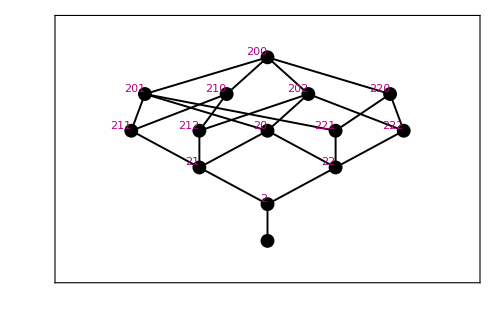

```mathematica
indices=IntervalP[fib205,{},{2,0,0}]
BuildSubPoset[fib205,indices,ideal205]
ChangeLabel[ideal205,Compact,1]
Diagram[ideal205,ShowLabels->1]
```

```mathematica
LatticeQ[ideal205]
DistributiveLatticeQ[ideal205]
```

True

False

For r > 1 the Fibonacci lattice F[r] is not distributive.

## 8. The "Poset Conjecture"

Recall that OmegaGF[P,q] is the rational generating function for the order polynomial of P.

Conjecture: For any poset P, the numerator of OmegaGF[p,q] has only real roots, and they are all nonpositive.

This was known as the Neggers Conjecture (after Neggers [1978]), or sometimes just the Poset Conjecture, until it was finally disproved in 2007 by John Stembridge.

We will illustrate the calculation on three random posets with 8 elements. Before Stembridge's counterexample, we might have considered this positive evidence for the conjecture.

Building poset testposet  ...

Done

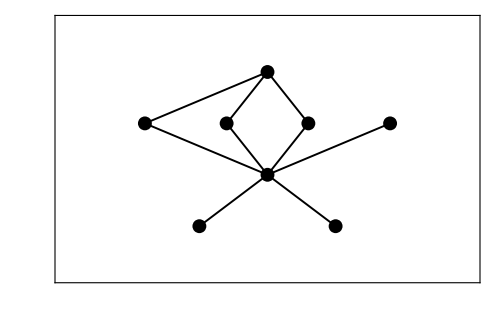

q==-6.60276||q==-1.||q==-0.80293||q==-0.0943119||q==0.

```mathematica
Build[RandomP[8,.5],testposet];
Diagram[testposet]
num=Numerator[OmegaGF[testposet,q]];
NRoots[num==0,q]
```

Building poset testposet  ...

Done

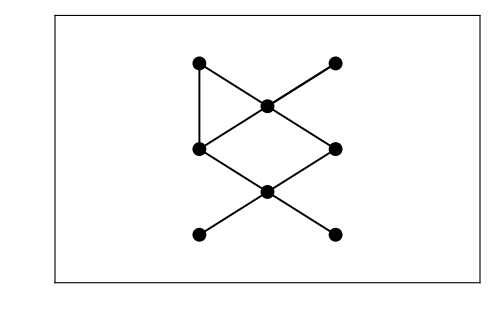

q==-6.60276||q==-1.||q==-0.80293||q==-0.0943119||q==0.

```mathematica
Build[RandomP[8,.5],testposet];
Diagram[testposet]
num=Numerator[OmegaGF[testposet,q]];
NRoots[num==0,q]
```

```mathematica
Build[RandomP[8,.3],testposet];
Diagram[testposet];
num=Numerator[OmegaGF[testposet,q]];
NRoots[num==0,q]
```

Building poset testposet  ...

Done

q==-6.60276||q==-1.||q==-0.80293||q==-0.0943119||q==0.

Stembridge showed that the smallest counterexamples to the Poset Conjecture have 17 elements. We conclude this section by constructing one of them.

```mathematica
stex = {{{1,3},{3,5},{5,7},{7,9},{9,11},{11,13},{13,15},{15,17},{2,4},{4,6},{6,8},{8,10},{10,12},{12,14},{14,16},
{1,12},{3,14},{5,16},{2,3},{4,5},{6,7},{8,9},{10,11},{12,13},{14,17}},17};
```

Building poset stem  ...

Done

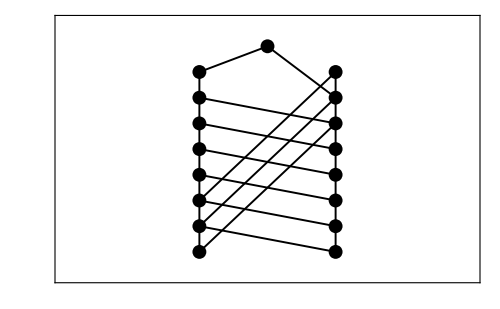

q+32 q^2+336 q^3+1420 q^4+2534 q^5+1946 q^6+658 q^7+86 q^8+3 q^9

q==-18.6404||q==-5.328||q==-1.85884-0.149768 ⅈ||q==-1.85884+0.149768 ⅈ||q==-0.561746||q==-0.24424||q==-0.111421||q==-0.0631306||q==0.

```mathematica
Build[stex,stem]
Diagram[stem,ShowLabels->True]
num=Numerator[OmegaGF[stem,q]]
NRoots[num==0,q]
```

## 9. The "Distributive Lattice Conjecture"

Let P be a poset with 0 and 1. Let ci(P) be the number of chains of length i from 0 to 1 in P (so, 
in particular, c0(P)=0 and c1(P)=1). Define the chain polynomial  of P by 
                                       C(P;q) = ∑i ≥ 1 ci(P) qi .

Conjecture: Let L be a distributive lattice. Then the polynomial C(L;q) has only real zeros.

This has come to be known as the Distributive Lattice Conjecture. As a matter of fact, it  is equivalent to the "Poset Conjecture" described in the previous section.  The reason is that  L = J(P) for some poset P, and it turns out that C(P;q) is related to OmegaGF(P;q) by a simple change of variables. We will illustrate this by computing both expressions for some randomly generated posets.

We can calculate C(P;q) using the "ChainsBetweenGF" command:

Building poset rand5  ...

Done

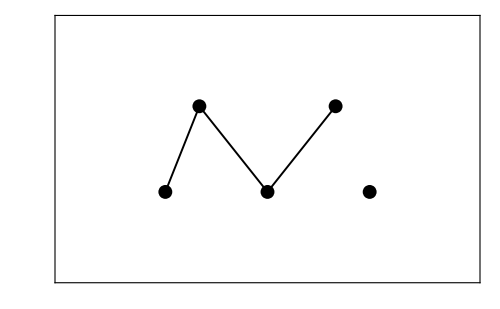

Building poset jprand5  ...

Done

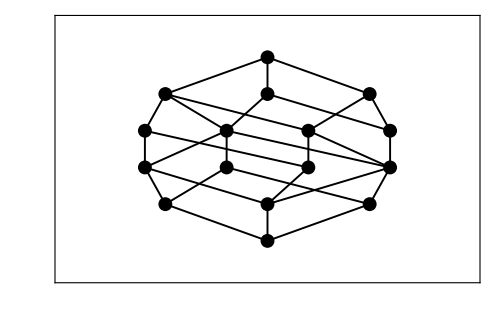

q+14 q^2+48 q^3+60 q^4+25 q^5

```mathematica
Build[RandomP[5,.3],rand5]
Diagram[rand5]
Build[JofP[rand5],jprand5]
Diagram[jprand5]
chainpoly=ChainsBetweenGF[jprand5,1,Card[jprand5]]
```

```mathematica
nn=Numerator[OmegaGF[rand5,q]]
```

q+10 q^2+12 q^3+2 q^4

```mathematica
Expand[Together[(nn/.q->t/(1+t)) (1+t)^5]]
```

t+14 t^2+48 t^3+60 t^4+25 t^5

```mathematica
NRoots[chainpoly==0,q]
```

q==-1.||q==-0.834017||q==-0.462222||q==-0.103761||q==0.

Building poset rand7  ...

Done

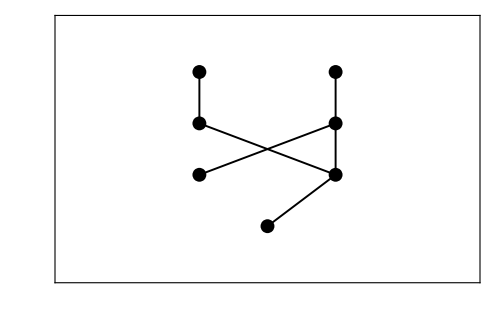

Building poset jprand7  ...

Done

q+14 q^2+66 q^3+146 q^4+167 q^5+96 q^6+22 q^7

```mathematica
Build[RandomP[7,.5],rand7]
Diagram[rand7]
Build[JofP[rand7],jprand7]
chainpoly=ChainsBetweenGF[jprand7,1,Card[jprand7]]
```

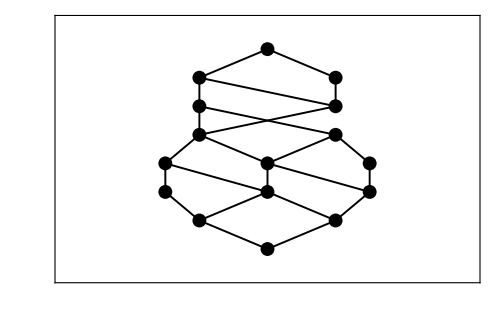

```mathematica
Diagram[jprand7]
```

```mathematica
NRoots[chainpoly==0,q]
```

q==-1.||q==-1.||q==-1.||q==-0.823497||q==-0.403263||q==-0.136876||q==0.

Again Stembridge' s counterexamples show that the Distributive Lattice Conjecture is false in general :

```mathematica
Build[JofP[stem],jpstem]
chainpoly=ChainsBetweenGF[jpstem,1,Card[jpstem]]
```

Building poset jpstem  ...

Done

q+48 q^2+936 q^3+10044 q^4+67950 q^5+313466 q^6+1035868 q^7+2530748 q^8+4661145 q^9+6538420 q^10+6999852 q^11+5683476 q^12+3442872 q^13+1508466 q^14+451880 q^15+82852 q^16+7016 q^17

```mathematica
NRoots[chainpoly==0,q]
```

q==-1.06658||q==-1.06252||q==-1.03417||q==-1.02636||q==-0.983865||q==-0.983659||q==-0.937142||q==-0.928866||q==-0.912186||q==-0.842022||q==-0.651166-0.0182745 ⅈ||q==-0.651165+0.0182753 ⅈ||q==-0.359691||q==-0.196297||q==-0.100251||q==-0.0593818||q==0.

## 10. Case Study: Zig-Zag Posets

Next we will perform an extended study of properties of a family of posets called (for obvious reasons) "zigzag posets".  Some of the observations made here were discovered using this package.

Building poset zz6  ...

Done

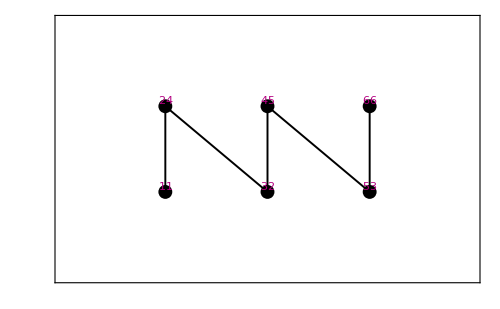

```mathematica
Build[ZigZag[6],zz6]
Diagram[zz6,ShowLabels->{1,2}]
```

Note that the red labels (on the left) are the elements of P[zz6] and the blue labels (on the right) are the indices of those elements. First we construct the lattice of order ideals of P[zz6] and compute its rank generating function.

Building poset jofzz6  ...

Done

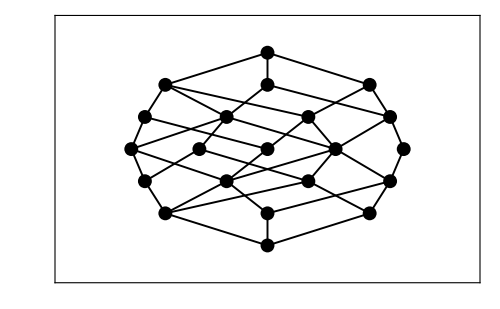

```mathematica
Build[JofP[zz6],jofzz6]
Diagram[jofzz6]
```

```mathematica
RGF[jofzz6]
```

1+3 q+4 q^2+5 q^3+4 q^4+3 q^5+q^6

A study of the roots of these polynomials led us to conjecture and prove (with Michelle Thompson) an explicit formula for the rank generating function. It can be expressed neatly in terms of Chebyshev polynomials:

```mathematica
Expand[q^3 ChebyshevU[3,1/2 (q+1+1/q)]]
```

1+3 q+4 q^2+5 q^3+4 q^4+3 q^5+q^6

Next we compute the linear extensions and topological sortings of P[zz5].

Building poset zz5  ...

Done

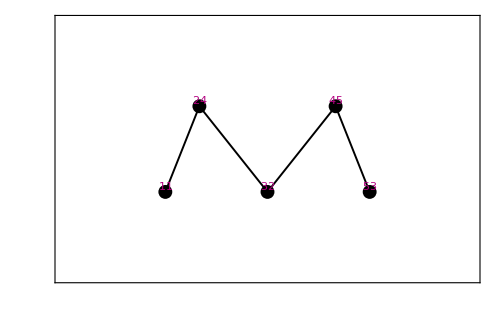

```mathematica
Build[ZigZag[5],zz5]
Diagram[zz5,ShowLabels->{1,2}]
```

```mathematica
LinearExtensions[zz5]
TopSortings[zz5]
```

{{4,2,1,5,3},{3,2,1,5,4},{3,2,1,4,5},{4,1,2,5,3},{3,1,2,5,4},{3,1,2,4,5},{2,1,4,3,5},{2,1,3,5,4},{2,1,3,4,5},{2,3,1,5,4},{2,3,1,4,5},{1,3,2,5,4},{1,3,2,4,5},{1,2,4,3,5},{1,2,3,5,4},{1,2,3,4,5}}

{{3,2,5,1,4},{3,2,1,5,4},{3,2,1,4,5},{2,3,5,1,4},{2,3,1,5,4},{2,3,1,4,5},{2,1,4,3,5},{2,1,3,5,4},{2,1,3,4,5},{3,1,2,5,4},{3,1,2,4,5},{1,3,2,5,4},{1,3,2,4,5},{1,2,4,3,5},{1,2,3,5,4},{1,2,3,4,5}}

These objects are essentially equivalent to alternating permutations, that is, permutations having the pattern a < b > c < d > e ...  , which are of great combinatorial interest. One way to see this is to observe that, if in each topological sorting, we map indices onto the original labels, we obtain a permutation in which the entries 1, 2, … have a “right-left-right-left ...”. pattern, and the inverses of such permutations are alternating in the usual sense.

```mathematica
tsort=TopSortings[zz5]/.{1->1,2->3,3->5,4->2,5->4}
Map[InversePermutation,tsort]
```

{{5,3,4,1,2},{5,3,1,4,2},{5,3,1,2,4},{3,5,4,1,2},{3,5,1,4,2},{3,5,1,2,4},{3,1,2,5,4},{3,1,5,4,2},{3,1,5,2,4},{5,1,3,4,2},{5,1,3,2,4},{1,5,3,4,2},{1,5,3,2,4},{1,3,2,5,4},{1,3,5,4,2},{1,3,5,2,4}}

{{4,5,2,3,1},{3,5,2,4,1},{3,4,2,5,1},{4,5,1,3,2},{3,5,1,4,2},{3,4,1,5,2},{2,3,1,5,4},{2,5,1,4,3},{2,4,1,5,3},{2,5,3,4,1},{2,4,3,5,1},{1,5,3,4,2},{1,4,3,5,2},{1,3,2,5,4},{1,5,2,4,3},{1,4,2,5,3}}

A famous result of D. Andre states that alternating permutations are enumerated by the Eulerian numbers. These are the number whose exponential generating function is Tan[x] + Sec[x] . Thus for example, for n=5,  we have

```mathematica
Length[LinearExtensions[zz5]]
```

16

```mathematica
D[(Tan[x]+Sec[x]), {x,5}]/.x->0
```

16

The subposet of WeakS[5] consisting of the topological sortings of P[zz5] has some interesting properties. In order to display it, we use the command LocateSet to find the indices of corresponding elements in WeakS[5].

Building poset weaks5  ...

Done

{11,22,25,41,44,45,63,64,67,68,85,86,89,102,103,114}

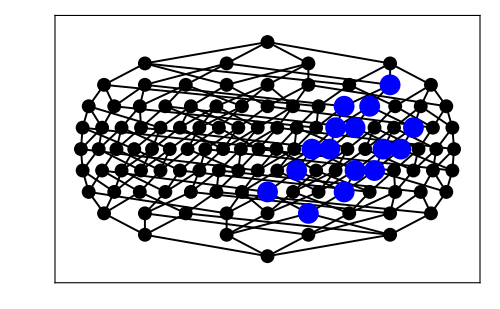

```mathematica
Build[WeakS[5],weaks5]
indices=LocateSet[weaks5,tsort]
Diagram[weaks5,indices]
```

This subposet is actually an interval in P[weaks5],  i.e. it consists of all elements lying between two fixed elements.  This property is somewhat difficult to verify visually, and the following test can be used to confirm it:

```mathematica
IntervalQ[weaks5,indices]
indices==IntervalP[weaks5,P[weaks5]⟦11⟧,P[weaks5]⟦114⟧]
```

True

True

The observation just made follows from a more general result due to Björner and Wachs ("Permutation statistics and linear extensions of posets", Jour. Combinatorial Theory A 57 (1991)).

Next we extract the sub-poset and take a good look at it.

Building Subposet interval5  ...

Building poset interval5  ...

Done

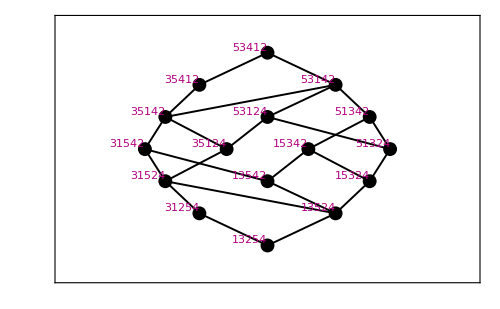

```mathematica
BuildSubPoset[weaks5,indices,interval5]
ChangeLabel[interval5,Compact,1]
Diagram[interval5,ShowLabels->1]
```

Next we compute number of maximal chains from the bottom element to each element of P.

```mathematica
MaximalChainsDown[interval5]
```

{1,1,1,2,1,1,3,2,2,1,5,3,3,5,11,16}

Is it a coincidence that the number (16) of maximal chains from bottom to top in the interval of topological sortings of P[ZigZag[5]] is equal to the total number of such topological sortings (16)?  Yes (unfortunately) this is a coincidence, and is not true in general. However, another similar numerical observation turns out not to be a coincidence. 

We compute the number of maximal chains from bottom to top in P[weaks4], a poset with very different structure. This number also equals 16 -- and this is a theorem.

Building poset weaks4  ...

Done

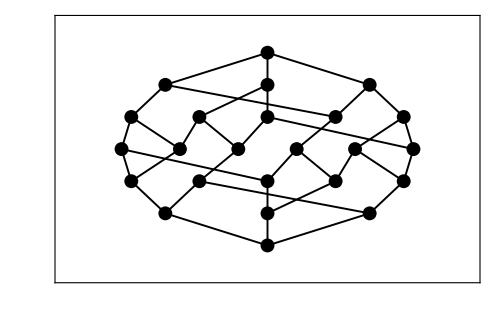

{1,1,1,1,1,2,1,1,1,2,1,2,2,2,1,3,3,3,2,3,5,6,5,16}

```mathematica
Build[WeakS[4],weaks4]
Diagram[weaks4]
MaximalChainsDown[weaks4]
```

Theorem:  the number of maximal chains in the interval of topological sortings of P[ZigZag[n]] in the weak order of S_n is equal to the number of maximal chains in S_(n-1) .

Another illustration (with n=6) of this phenomenon:

```mathematica
Build[ZigZag[6],zz6]
tsort6=TopSortings[zz6]/.{1->1,2->3,3->5,4->2,5->4,6->6}
Build[WeakS[6],weaks6]
indices6=LocateSet[weaks6,tsort6];
IntervalQ[weaks6,indices6]
BuildSubPoset[weaks6,indices6,interval6]
MaximalChainsDown[interval6]//Last
```

Building poset zz6  ...

Done

{{5,6,3,4,1,2},{5,3,6,4,1,2},{5,3,4,6,1,2},{5,3,4,1,6,2},{5,3,4,1,2,6},{5,6,3,1,4,2},{5,3,6,1,4,2},{5,3,1,6,4,2},{5,3,1,4,6,2},{5,3,1,4,2,6},{5,6,3,1,2,4},{5,3,6,1,2,4},{5,3,1,6,2,4},{5,3,1,2,6,4},{5,3,1,2,4,6},{3,5,6,4,1,2},{3,5,4,6,1,2},{3,5,4,1,6,2},{3,5,4,1,2,6},{3,5,6,1,4,2},{3,5,1,6,4,2},{3,5,1,4,6,2},{3,5,1,4,2,6},{3,5,6,1,2,4},{3,5,1,6,2,4},{3,5,1,2,6,4},{3,5,1,2,4,6},{3,1,2,5,6,4},{3,1,2,5,4,6},{3,1,5,6,4,2},{3,1,5,4,6,2},{3,1,5,4,2,6},{3,1,5,6,2,4},{3,1,5,2,6,4},{3,1,5,2,4,6},{5,6,1,3,4,2},{5,1,6,3,4,2},{5,1,3,6,4,2},{5,1,3,4,6,2},{5,1,3,4,2,6},{5,6,1,3,2,4},{5,1,6,3,2,4},{5,1,3,6,2,4},{5,1,3,2,6,4},{5,1,3,2,4,6},{1,5,6,3,4,2},{1,5,3,6,4,2},{1,5,3,4,6,2},{1,5,3,4,2,6},{1,5,6,3,2,4},{1,5,3,6,2,4},{1,5,3,2,6,4},{1,5,3,2,4,6},{1,3,2,5,6,4},{1,3,2,5,4,6},{1,3,5,6,4,2},{1,3,5,4,6,2},{1,3,5,4,2,6},{1,3,5,6,2,4},{1,3,5,2,6,4},{1,3,5,2,4,6}}

Building poset weaks6  ...

Done

True

Building Subposet interval6  ...

Building poset interval6  ...

Done

768

```mathematica
Build[WeakS[5],weaks5]
MaximalChainsDown[weaks5]//Last
```

Building poset weaks5  ...

Done

768

## 11. Case Study: 2-Rowed Standard Young Tableaux

This example illustrates an interesting poset whose elements correspond to 2-rowed standard tableaux. The ordering is defined by reading each tableau from left to right, top to bottom (the standard reading order), and considering these permutations as a subposet of the right weak order.

We illustrate this construction with tableaux of shape λ = {4,3}.

```mathematica
st43 = STableaux[{4,3}];
Map[Grid,st43]
perms43 = Map[Flatten,st43]
```

{1 | 2 | 3 | 4
5 | 6 | 7 | ,1 | 2 | 3 | 5
4 | 6 | 7 | ,1 | 2 | 3 | 6
4 | 5 | 7 | ,1 | 2 | 3 | 7
4 | 5 | 6 | ,1 | 2 | 4 | 5
3 | 6 | 7 | ,1 | 2 | 4 | 6
3 | 5 | 7 | ,1 | 2 | 4 | 7
3 | 5 | 6 | ,1 | 2 | 5 | 6
3 | 4 | 7 | ,1 | 2 | 5 | 7
3 | 4 | 6 | ,1 | 3 | 4 | 5
2 | 6 | 7 | ,1 | 3 | 4 | 6
2 | 5 | 7 | ,1 | 3 | 4 | 7
2 | 5 | 6 | ,1 | 3 | 5 | 6
2 | 4 | 7 | ,1 | 3 | 5 | 7
2 | 4 | 6 | }

{{1,2,3,4,5,6,7},{1,2,3,5,4,6,7},{1,2,3,6,4,5,7},{1,2,3,7,4,5,6},{1,2,4,5,3,6,7},{1,2,4,6,3,5,7},{1,2,4,7,3,5,6},{1,2,5,6,3,4,7},{1,2,5,7,3,4,6},{1,3,4,5,2,6,7},{1,3,4,6,2,5,7},{1,3,4,7,2,5,6},{1,3,5,6,2,4,7},{1,3,5,7,2,4,6}}

Building poset ws7  ...

Done

{1,5,22,23,67,68,71,161,163,164,326,327,330,583}

Building Subposet poset43  ...

Building poset poset43  ...

Done

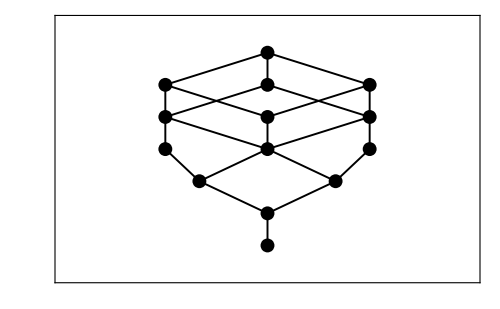

```mathematica
Build[RWeakS[7],ws7]
ind43=LocateSet[ws7,perms43]
BuildSubPoset[ws7,ind43,poset43]
Diagram[poset43]
```

Next, we' ll illustrate some complicated manipulation of labels.  At this point P[poset43] contains a list the permutations that were used to define the sub-order of RWeakS[7], and these are also mirrored in Labels[poset43][[1]].

```mathematica
P[poset43]
```

{{1,2,3,4,5,6,7},{1,2,3,5,4,6,7},{1,2,4,5,3,6,7},{1,2,3,6,4,5,7},{1,3,4,5,2,6,7},{1,2,4,6,3,5,7},{1,2,3,7,4,5,6},{1,3,4,6,2,5,7},{1,2,5,6,3,4,7},{1,2,4,7,3,5,6},{1,3,5,6,2,4,7},{1,3,4,7,2,5,6},{1,2,5,7,3,4,6},{1,3,5,7,2,4,6}}

It will be convenient to access these in their original tableau form, so we will redefine Labels[poset43][[1]] as tableaux.

```mathematica
ChangeLabel[poset43,Tabify[#,{4,3}]&,1]
Labels[poset43][[1]]
```

{{{1,2,3,4},{5,6,7}},{{1,2,3,5},{4,6,7}},{{1,2,4,5},{3,6,7}},{{1,2,3,6},{4,5,7}},{{1,3,4,5},{2,6,7}},{{1,2,4,6},{3,5,7}},{{1,2,3,7},{4,5,6}},{{1,3,4,6},{2,5,7}},{{1,2,5,6},{3,4,7}},{{1,2,4,7},{3,5,6}},{{1,3,5,6},{2,4,7}},{{1,3,4,7},{2,5,6}},{{1,2,5,7},{3,4,6}},{{1,3,5,7},{2,4,6}}}

We would also like to display these tableaux in compact form, so we' ll redefine Labels[poset43][[2]] as actual tableaux.

```mathematica
ChangeLabel[poset43,P[poset43],2]
ChangeLabel[poset43,Tabify[#,{4,3}]&,2]
ChangeLabel[poset43,Grid,2]
Labels[poset43][[2]]
```

{1 | 2 | 3 | 4
5 | 6 | 7 | ,1 | 2 | 3 | 5
4 | 6 | 7 | ,1 | 2 | 4 | 5
3 | 6 | 7 | ,1 | 2 | 3 | 6
4 | 5 | 7 | ,1 | 3 | 4 | 5
2 | 6 | 7 | ,1 | 2 | 4 | 6
3 | 5 | 7 | ,1 | 2 | 3 | 7
4 | 5 | 6 | ,1 | 3 | 4 | 6
2 | 5 | 7 | ,1 | 2 | 5 | 6
3 | 4 | 7 | ,1 | 2 | 4 | 7
3 | 5 | 6 | ,1 | 3 | 5 | 6
2 | 4 | 7 | ,1 | 3 | 4 | 7
2 | 5 | 6 | ,1 | 2 | 5 | 7
3 | 4 | 6 | ,1 | 3 | 5 | 7
2 | 4 | 6 | }

```mathematica
Diagram[poset43,Manipulate->True,BackGround2->Yellow]
```

12345

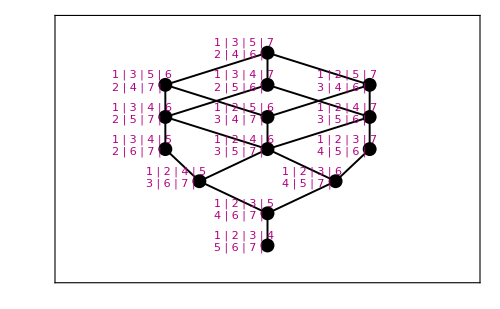

```mathematica
Diagram[poset43,ShowLabels->True]
```

Next we’ll separate the tableaux into two classes, according to whether the largest number is in the first row or the second, and display those in the first class as "special" points.

```mathematica
tabs = Labels[poset43][[1]]
firstrow = Select[tabs,MemberQ[#[[1]],7]&]
firstpos=Table[Position[tabs,firstrow[[j]]],{j,Length[firstrow]}]//Flatten
```

{{{1,2,3,4},{5,6,7}},{{1,2,3,5},{4,6,7}},{{1,2,4,5},{3,6,7}},{{1,2,3,6},{4,5,7}},{{1,3,4,5},{2,6,7}},{{1,2,4,6},{3,5,7}},{{1,2,3,7},{4,5,6}},{{1,3,4,6},{2,5,7}},{{1,2,5,6},{3,4,7}},{{1,2,4,7},{3,5,6}},{{1,3,5,6},{2,4,7}},{{1,3,4,7},{2,5,6}},{{1,2,5,7},{3,4,6}},{{1,3,5,7},{2,4,6}}}

{{{1,2,3,7},{4,5,6}},{{1,2,4,7},{3,5,6}},{{1,3,4,7},{2,5,6}},{{1,2,5,7},{3,4,6}},{{1,3,5,7},{2,4,6}}}

{7,10,12,13,14}

```mathematica
Diagram[poset43,firstpos,Manipulate->True]
```

12345

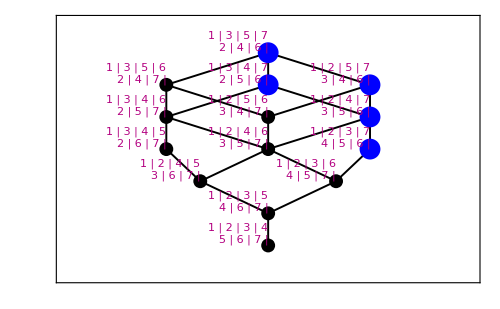

```mathematica
Diagram[poset43,firstpos,ShowLabels->2]
```

The selected elements form an interval subposet :

```mathematica
IntervalQ[poset43,firstpos]
```

True

It is interesting that 2-row tableaux posets are always distributive lattices.

```mathematica
DistributiveLatticeQ[poset43]
```

True

Also, the ordering on tableaux is identical to that induced by the strong order on permutations.

```mathematica
Build[StrongS[7],ss7]
ind43s=LocateSet[ss7,perms43]
BuildSubPoset[ss7,ind43s,sposet43]
```

Building poset ss7  ...

Done

{1,5,20,23,54,66,71,144,159,164,306,311,330,569}

Building Subposet sposet43  ...

Building poset sposet43  ...

Done

```mathematica
Diagram[sposet43]
```

-Graphics-

```mathematica
IsomorphicQ[poset43,sposet43]
P[poset43]==P[sposet43]
CoverRelations[poset43]==CoverRelations[sposet43]
```

True

True

True

Neither of the last two stated properties is true for posets constructed using tableaux with more than two rows.

Example :

```mathematica
st321 = STableaux[{3,2,1}];
Map[Grid,st321]
perms321 = Map[Flatten,st321];
```

{1 | 2 | 3
4 | 5 | 
6 |  | ,1 | 2 | 3
4 | 6 | 
5 |  | ,1 | 2 | 4
3 | 5 | 
6 |  | ,1 | 2 | 4
3 | 6 | 
5 |  | ,1 | 2 | 5
3 | 4 | 
6 |  | ,1 | 2 | 6
3 | 4 | 
5 |  | ,1 | 2 | 5
3 | 6 | 
4 |  | ,1 | 2 | 6
3 | 5 | 
4 |  | ,1 | 3 | 4
2 | 5 | 
6 |  | ,1 | 3 | 4
2 | 6 | 
5 |  | ,1 | 3 | 5
2 | 4 | 
6 |  | ,1 | 3 | 6
2 | 4 | 
5 |  | ,1 | 3 | 5
2 | 6 | 
4 |  | ,1 | 3 | 6
2 | 5 | 
4 |  | ,1 | 4 | 5
2 | 6 | 
3 |  | ,1 | 4 | 6
2 | 5 | 
3 |  | }

Building poset ws6  ...

Done

Building Subposet poset321  ...

Building poset poset321  ...

Done

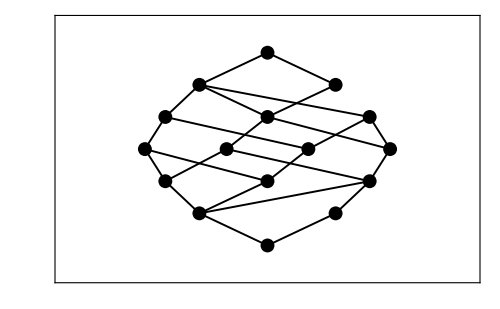

```mathematica
Build[RWeakS[6],ws6]
ind321=LocateSet[ws6,perms321];
BuildSubPoset[ws6,ind321,poset321]
Diagram[poset321]
```

```mathematica
DistributiveLatticeQ[poset321]
```

False

Building poset ss6  ...

Done

Building Subposet sposet321  ...

Building poset sposet321  ...

Done

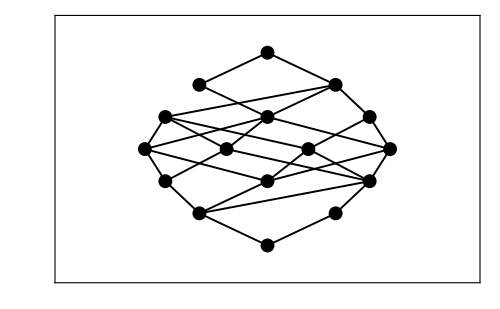

```mathematica
Build[StrongS[6],ss6]
ind321s=LocateSet[ss6,perms321];
BuildSubPoset[ss6,ind321s,sposet321]
Diagram[sposet321]
```

```mathematica
IsomorphicQ[poset321,sposet321]
```

Different number of CoverRelations.

False

## 12. “Rowmotion”

We illustrate an interesting map on the ideals of a poset that has been studied by various people (Brouwer-Schriver, Cameron-Fon Der Flass, Panyushev, Armstrong-Stump-Thomas, Striker-Williams, Roby-Propp).

One defines a bijective map T: J[P] ⟶ J[P] on ideals of P, as follows: if I is an ideal, then T[I] is the ideal generated by the minimal elements of the complement of P.

The orbit structure of T has proved to be of great interest.  For example, Propp and Roby have shown that, if P is a product of chains, then the average size of an ideal is independent of the orbit.  We illustrate their result with the poset Chain[3]× Chain[4].

```mathematica
T[name_,ideal_] := OrderIdeal[name,MinElements[name,Complement[Range[Card[name]],ideal]]]
```

Building poset cp34  ...

Done

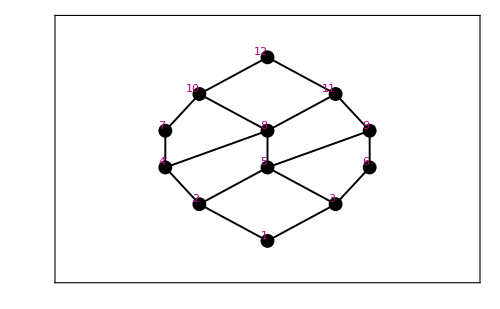

```mathematica
Build[CP[Chain[3],Chain[4]],cp34]
Diagram[cp34,ShowLabels->2]
```

```mathematica
T[cp34,{1,2,3,4,6}]
```

{1,2,3,4,5,7}

```mathematica
orbit[name_,ideal_] := Module[{orb={ideal},next},
next = T[name,ideal];
While[next ≠ideal,orb = Append[orb,next];next = T[name,next]];
orb
]
```

```mathematica
orb12346=orbit[cp34,{1,2,3,4,6}]
Apply[Plus,Map[Length,%]]/Length[%]
```

{{1,2,3,4,6},{1,2,3,4,5,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,8},{1,2,3,4,6,7},{1,2,3,5}}

6

```mathematica
orb1=orbit[cp34,{1}]
Apply[Plus,Map[Length,%]]/Length[%]
```

{{1},{1,2,3},{1,2,3,4,5,6},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{}}

6

```mathematica
orb12=orbit[cp34,{1,2}]
Apply[Plus,Map[Length,%]]/Length[%]
```

{{1,2},{1,2,3,4},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,7,8,9,11},{1,2,3,4,5,7,8,10},{1,3,6}}

6

```mathematica
orb13=orbit[cp34,{1,3}]
Apply[Plus,Map[Length,%]]/Length[%]
```

{{1,3},{1,2,3,6},{1,2,3,4,5},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,8,9,11},{1,2,4,7}}

6

```mathematica
orb124=orbit[cp34,{1,2,4}]
Apply[Plus,Map[Length,%]]/Length[%]
```

{{1,2,4},{1,2,3,4,7},{1,2,3,5,6},{1,2,3,4,5,6,9},{1,2,3,4,5,7,8},{1,2,3,4,5,6,7,8,10},{1,2,3,5,6,9}}

6

Check to see that we have all of the orbits :

```mathematica
Join[orb1,orb12,orb13,orb124,orb12346]//Sort
%==(OrderIdeals[cp34]//Sort)
```

{{},{1},{1,2},{1,3},{1,2,3},{1,2,4},{1,3,6},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,7},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,5,6},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,6,7},{1,2,3,5,6,9},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,7,8},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,8,9,11},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,11},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12}}

True

Here' s a larger example, with animation.

Building poset cp711  ...

Done

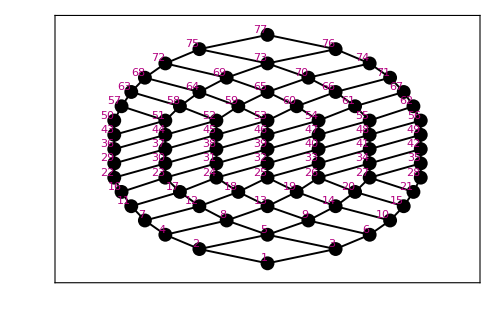

77/2

```mathematica
Build[CP[Chain[7],Chain[11]],cp711]
Diagram[cp711,ShowLabels->2]
orb=orbit[cp711,OrderIdeal[cp711,{17,29}]];
Apply[Plus,Map[Length,%]]/Length[%]
Manipulate[Diagram[cp711,MaxElements[cp711,orb[[k]]]],{k,1,Length[orb],1}]
```

## 13. The Complete Repertoire

We conclude by taking a very simple poset (P =[ZigZag[4]) and applying almost every command to either P or J(P).

```mathematica
Build[ZigZag[4],zz4]
Build[JofP[zz4],jofzz4]
```

Building poset zz4  ...

Done

Building poset jofzz4  ...

Done

```mathematica
P[jofzz4]
PGraded[jofzz4]
```

{{},{3},{4},{1,3},{3,4},{1,3,4},{2,3,4},{1,2,3,4}}

{{{}},{{3},{4}},{{1,3},{3,4}},{{1,3,4},{2,3,4}},{{1,2,3,4}}}

```mathematica
RankedQ[jofzz4]
Rank[jofzz4]
NK[jofzz4]
RGF[jofzz4]
```

True

{0,1,1,2,2,3,3,4}

{1,2,2,2,1}

1+2 q+2 q^2+2 q^3+q^4

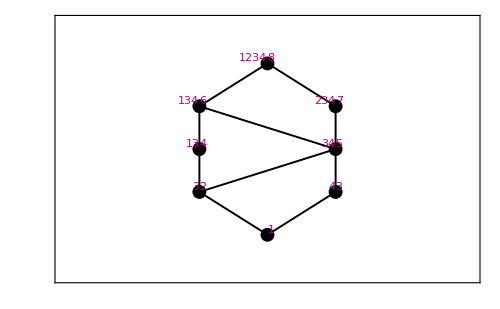

```mathematica
ChangeLabel[jofzz4,Compact,1]
Diagram[jofzz4,ShowLabels->{1,2}]
```

```mathematica
SpecialPoints[jofzz4,MemberQ[#,1]&]
```

{4,6,8}

{6,7}

{{1,2},{2,4},{3,5},{4,6},{5,7},{7,8}}

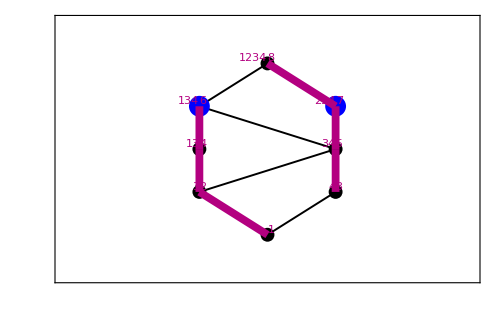

```mathematica
points=MaxAntichain[jofzz4]
links=DilworthCover[jofzz4]
Diagram[jofzz4,points,links,ShowLabels->{1,2}]
```

```mathematica
Diagram[jofzz4,points,links,Manipulate->True];
```

```mathematica
Fuse[DilworthCover[jofzz4]] (*Combines links into chains *)
```

{{1,2,4,6},{3,5,7,8}}

```mathematica
JoinSubLatticeQ[jofzz4,{2,4,5,7}]
MeetSubLatticeQ[jofzz4,{2,4,5,7}]
```

False

True

```mathematica
indices=JoinSubLattice[jofzz4,{2,4,5,7}]
BuildSubPoset[jofzz4,indices,jsub]
Diagram[jsub,Manipulate->True];
```

{2,4,5,6,7,8}

Building Subposet jsub  ...

Building poset jsub  ...

Done

```mathematica
Ups[jofzz4]
Downs[jofzz4]
StrictUps[jofzz4]
StrictDowns[jofzz4]
```

{{1,2,3,4,5,6,7,8},{2,4,5,6,7,8},{3,5,6,7,8},{4,6,8},{5,6,7,8},{6,8},{7,8},{8}}

{{1},{1,2},{1,3},{1,2,4},{1,2,3,5},{1,2,3,4,5,6},{1,2,3,5,7},{1,2,3,4,5,6,7,8}}

{{2,3,4,5,6,7,8},{4,5,6,7,8},{5,6,7,8},{6,8},{6,7,8},{8},{8},{}}

{{},{1},{1},{1,2},{1,2,3},{1,2,3,4,5},{1,2,3,5},{1,2,3,4,5,6,7}}

```mathematica
CoverRelations[jofzz4]
Covers[jofzz4]
UpDegree[jofzz4]
CoCovers[jofzz4]
DownDegree[jofzz4]
```

{{1,2},{1,3},{2,4},{2,5},{3,5},{4,6},{5,6},{5,7},{6,8},{7,8}}

{{2,3},{4,5},{5},{6},{6,7},{8},{8},{}}

{2,2,1,1,2,1,1,0}

{{},{1},{1},{2},{2,3},{4,5},{5},{6,7}}

{0,1,1,1,2,2,1,2}

```mathematica
OrderIdeals[jofzz4]
Map[MaxElements[jofzz4,#]&,%]
```

{{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7},{1,2,3,4,5,7},{1,2,3,4,5,6},{1,2,3,5,7},{1,2,3,4,5},{1,2,3,5},{1,2,3,4},{1,2,4},{1,2,3},{1,3},{1,2},{1},{}}

{{8},{6,7},{4,7},{6},{7},{4,5},{5},{3,4},{4},{2,3},{3},{2},{1},{}}

```mathematica
DualOrderIdeals[jofzz4]
Map[MinElements[jofzz4,#]&,%]
```

{{},{8},{6,8},{7,8},{4,6,8},{6,7,8},{4,6,7,8},{5,6,7,8},{3,5,6,7,8},{4,5,6,7,8},{2,4,5,6,7,8},{3,4,5,6,7,8},{2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8}}

{{},{8},{6},{7},{4},{6,7},{4,7},{5},{3},{4,5},{2},{3,4},{2,3},{1}}

```mathematica
MatrixForm[ZetaP[jofzz4]]
MatrixForm[Mu[jofzz4]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | -1 | -1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | -1 | -1 | 1 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
ToRelation[ZetaP[jofzz4]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,2},{2,4},{2,5},{2,6},{2,7},{2,8},{3,3},{3,5},{3,6},{3,7},{3,8},{4,4},{4,6},{4,8},{5,5},{5,6},{5,7},{5,8},{6,6},{6,8},{7,7},{7,8},{8,8}}

```mathematica
MaximalChainsUp[jofzz4]
MaximalChainsDown[jofzz4]
LinearExtensions[zz4]
TopSortings[zz4]
```

{5,3,2,1,2,1,1,1}

{1,1,1,1,2,3,2,5}

{{3,1,4,2},{2,1,4,3},{2,1,3,4},{1,2,4,3},{1,2,3,4}}

{{2,4,1,3},{2,1,4,3},{2,1,3,4},{1,2,4,3},{1,2,3,4}}

```mathematica
ChainsBetweenGF[jofzz4,1,Card[jofzz4]]
```

q+6 q^2+10 q^3+5 q^4

```mathematica
Together[ZetaPoly[jofzz4]]
Together[Omega[zz4,n]]
```

1/24 (2 n+7 n^2+10 n^3+5 n^4)

1/24 (2 n+7 n^2+10 n^3+5 n^4)

```mathematica
OmegaGF[zz4,q]
OmegaBarGF[zz4,q]
```

(q+3 q^2+q^3)/(1-q)^5

(q^2+3 q^3+q^4)/(1-q)^5

```mathematica
G[zz4,q]
GBar[zz4,q]
```

(1+q+q^2+q^3+q^4)/((1-q) (1-q^2) (1-q^3) (1-q^4))

(q^2+q^3+q^4+q^5+q^6)/((1-q) (1-q^2) (1-q^3) (1-q^4))

```mathematica
LatticeQ[jofzz4]
MatrixForm[LJoin[jofzz4]]
MatrixForm[LMeet[jofzz4]]
```

True

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
2 | 2 | 5 | 4 | 5 | 6 | 7 | 8
3 | 5 | 3 | 6 | 5 | 6 | 7 | 8
4 | 4 | 6 | 4 | 6 | 6 | 8 | 8
5 | 5 | 5 | 6 | 5 | 6 | 7 | 8
6 | 6 | 6 | 6 | 6 | 6 | 8 | 8
7 | 7 | 7 | 8 | 7 | 8 | 7 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8)

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 2 | 2 | 2 | 2
1 | 1 | 3 | 1 | 3 | 3 | 3 | 3
1 | 2 | 1 | 4 | 2 | 4 | 2 | 4
1 | 2 | 3 | 2 | 5 | 5 | 5 | 5
1 | 2 | 3 | 4 | 5 | 6 | 5 | 6
1 | 2 | 3 | 2 | 5 | 5 | 7 | 7
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8)

Building poset bigger  ...

Done

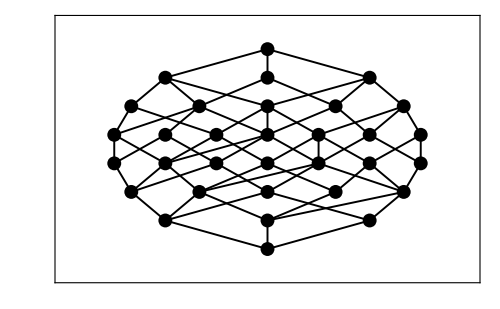

```mathematica
Build[CP[jofzz4,Chain[4]],bigger]
Diagram[bigger]
```

Building Subposet joinirreducibles  ...

Building poset joinirreducibles  ...

Done

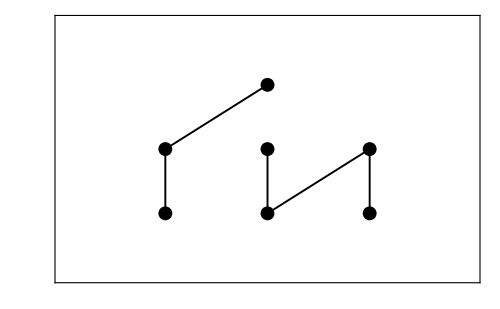

```mathematica
BuildSubPoset[bigger,JI[bigger],joinirreducibles]
Diagram[joinirreducibles]
```

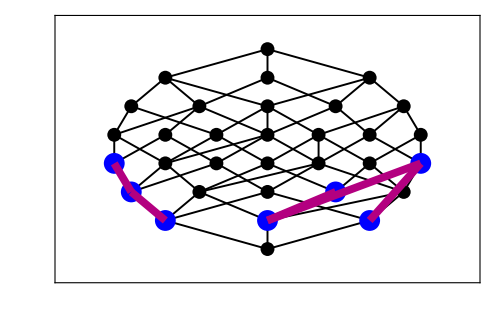

```mathematica
Diagram[bigger,JI[bigger],JICoverRelations[bigger]]
```

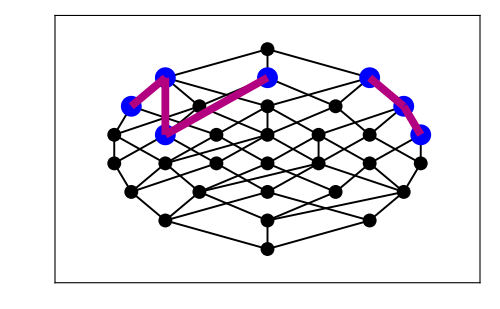

```mathematica
Diagram[bigger,MI[bigger],MICoverRelations[bigger]]
```

```mathematica
MatrixForm[ZetaMI[bigger]]
```

(1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

Building poset jofzz4dual  ...

Done

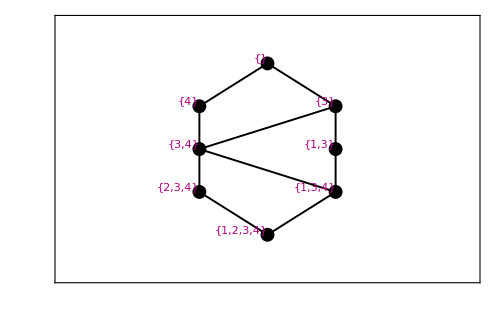

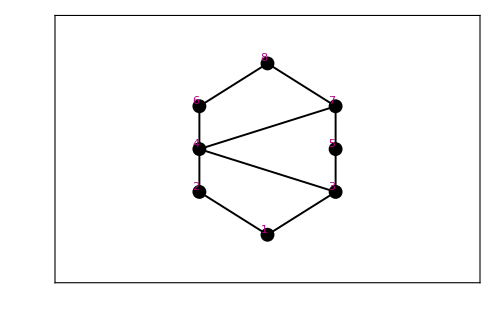

```mathematica
BuildDual[jofzz4,jofzz4dual]
Diagram[jofzz4dual,ShowLabels->1]
Diagram[jofzz4dual,ShowLabels->2]
```

```mathematica
IsomorphicQ[jofzz4,jofzz4dual]
```

True

```mathematica
Zap[zz4]
Zap[jofzz4]
```

## 14. Catalog of Small Posets and Lattices

Along with the package itself, we have supplied two more files, allposets1-7.txt and alllattices1-9.txt.  These contain descriptions of all non-isomorphic posets of size ≤ 7, and all non-isomorphic lattices of size ≤ 9. They were generated using John Stembridge's Maple package for posets, and then translated into Mathematica format.

This data can be accessed as follows. First be sure that the two files are in a directory that Mathematica searches when input is requested (for example, the AddOns/ExtraPackages folder in the PC version). Then, for example, execute

```mathematica
<<allposets1-7.txt;
```

The data is now recorded in a variable called AllPosets. For example, AllPosets[3] is a list of all posets of size 3.  Each entry consists of a list of relations.  Thus, to build the kth poset, one executes the command Build[{AllPosets[3][[k]],3}].

```mathematica
AllPosets[3]
```

{{},{{1,2}},{{1,3},{2,3}},{{1,2},{2,3}},{{1,2},{1,3}}}

Building poset sample  ...

Done

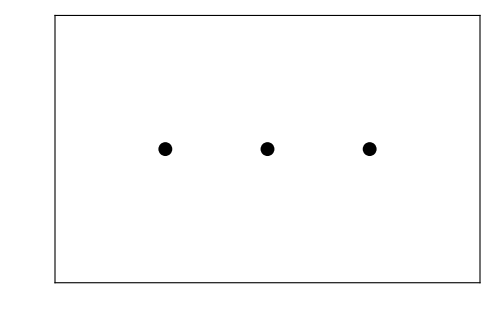

Building poset sample  ...

Done

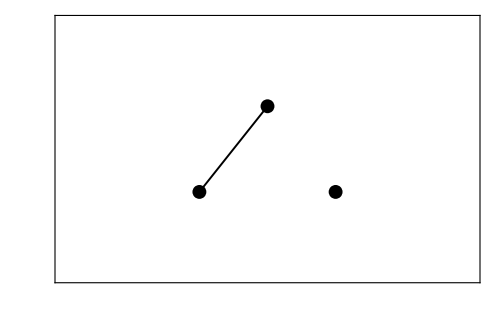

Building poset sample  ...

Done

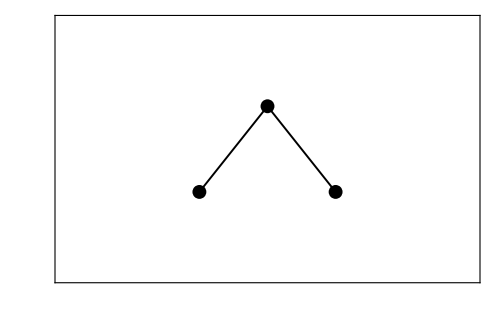

Building poset sample  ...

Done

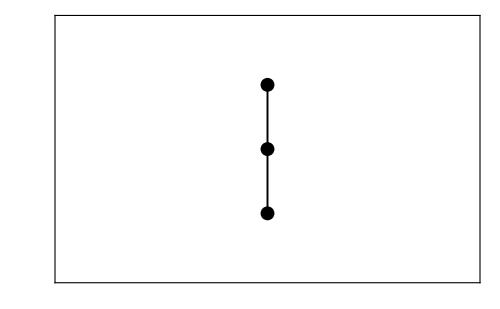

Building poset sample  ...

Done

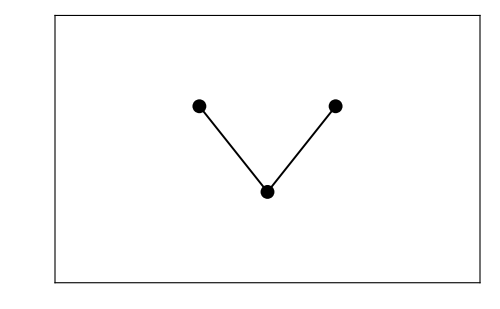

```mathematica
For[k=1,k≤5,k++,Build[{AllPosets[3]⟦k⟧,3},sample];Diagram[sample]//Print]
```

The command NumPosets assumes that allposets1-7 has been read, and returns the number of posets of each size. For example,

```mathematica
Table[NumPosets[n],{n,1,7}]
```

{1,2,5,16,63,318,2045}

Exercise:  check this sequence and the next one (lattices of size n, for 1 ⩽ n ≤ 9) by looking in Neil Sloane's book.

```mathematica
<<alllattices1-9.txt
```

```mathematica
Table[NumLattices[n],{n,1,9}]
```

{1,1,1,2,5,15,53,222,1078}

We can build all the posets of a size n and test them for various properties.  Beware that for large N this may consume a lot of memory.  We illustrate by checking all of the posets with 4 elements to be sure there that no two are isomorphic (output shortened to save space).

```mathematica
For[k=1,k≤16,k++,Build[{AllPosets[4]⟦k⟧,4},test[k]]]
```

Building poset test[1]  ...

Done

Building poset test[2]  ...

Done

...

Building poset test[15]  ...

Done

Building poset test[16]  ...

Done

```mathematica
For[j=1,j≤16,j++,For[k=j+1,k≤16,k++,Print["------------------------"];Print["Testing posets ",j,", ",k];If[IsomorphicQ[test[j],test[k]],Print["***** Posets ",j," and ",k," are isomorphic!"]];]]
```

------------------------

------------------------
Testing posets 1, 2
Different number of CoverRelations.
------------------------
Testing posets 1, 3
Different number of CoverRelations.
------------------------
Testing posets 1, 4
Different number of CoverRelations.
------------------------
Testing posets 1, 5
Different number of CoverRelations.
------------------------
.
.
.
------------------------
Testing posets 6, 9
Different number of CoverRelations.
------------------------
Testing posets 6, 10
UpDegree distribution is different.
------------------------
Testing posets 6, 11
UpDegree distribution is different.
------------------------
.
.
.
------------------------
Testing posets 9, 16
Different number of CoverRelations.
------------------------
Testing posets 10, 11
Number of ones in Zeta matrix is different.
------------------------
Testing posets 10, 12
DownDegree distribution is different.
------------------------
Testing posets 10, 13
UpDegree distribution is different.
------------------------
Testing posets 10, 14
UpDegree distribution is different.
------------------------
Testing posets 10, 15
Different number of CoverRelations.
------------------------
.
.
.
------------------------
Testing posets 13, 15
Different number of CoverRelations.
------------------------
Testing posets 13, 16
UpDegree distribution is different.
------------------------
Testing posets 14, 15
Different number of CoverRelations.
------------------------
Testing posets 14, 16
UpDegree distribution is different.
------------------------
Testing posets 15, 16
Different number of CoverRelations.

## Appendix: List of All Commands

For more information about a particular command, type

```mathematica
Information["<command>",LongForm->False]
```

For example:

```mathematica
Information["DownDegree",LongForm->False]
```

DownDegree[name][[x]] is the number of 
elements covered by P[name][[x]].

To see a list of all Poset commands containing a particular string, type

```mathematica
ListCommands["string"]
```

or

```mathematica
Information["Posets`*string*",LongForm->True]
```

For example:

```mathematica
ListCommands["Chain"]
```

(Chain | MaximalChainsDown
ChainsBetweenGF | MaximalChainsUp
LongestChain | ---)

For a complete list of all commands known to Posets, type

```mathematica
ListCommands[]
```

(AllTableaux | MeetSubLattice
AMAJ | MeetSubLatticeQ
Antichain | MI
ASC | MICoverRelations
Background1 | MinElements
Background2 | MSL
Build | Mu
BuildDual | NewLabel
BuildSubPoset | NK
Card | NonXP
Chain | NumLattices
ChainsBetweenGF | NumP
ChangeLabel | NumPosets
CharPoly | Omega
CleanRank | OmegaBar
CoCovers | OmegaBarGF
Compact | OmegaGF
ContractionLattice | OrderIdeal
CoverRelations | OrderIdealQ
Covers | OrderIdeals
CP | OrdinalSum
CProduct | OS
DES | P
Diagram | PGraded
DilworthCover | PGradedIndices
DisjointSum | PolyToGF
DistributiveLatticeQ | PosetP
Div | RandomP
DownDegree | Rank
Downs | RankedQ
DS | ResetLabel
DualOrderIdeal | RGF
DualOrderIdealQ | RWeakS
DualOrderIdeals | SavedSettings
Ferrers | SaveOne
Fuse | SetP
G | Sets
GBar | ShowLabels
GenFun | Silent
GetIsomorphism | SL
GFToPoly | SortByRanks
H | SP
InfiniteProduct | SpecialPoints
IntervalP | SPM
IntervalQ | STableaux
InversionCode | StrictDowns
IsomorphicQ | StrictUps
JI | StrongRankedQ
JICoverRelations | StrongS
JofP | SubLattice
JoinL | SubLatticeQ
JoinSubLattice | Subwords
JoinSubLatticeQ | Tabify
JSL | TClosure
L | TensorProduct
Labels | ToMatrix
LatticeQ | ToPermutation
LinearExtensions | TopSort
ListCommands | TopSortings
LJoin | ToRelation
LMeet | UpDegree
LocateElement | Ups
LocateSet | Ver
LongestChain | WeakS
L$ | YoungsLattice
MAJ | Zap
MajP | ZeroDiffs
MaxAntichain | ZetaJI
MaxElements | ZetaMI
MaximalChainsDown | ZetaP
MaximalChainsUp | ZetaPoly
MeetL | ZigZag)

For more information about each command, please consult the "usage" section of the package. This  gives the precise syntax for each command, and can even be printed out as a compact "user's manual", if desired.